```mathematica
box[x_,q_]:=(
(q^(x/2)-q^(-x/2))/(q^(1/2)-q^(-1/2))
);
```

```mathematica
capacityChernSimons[a_,b_,Ni_,k_]:=(
q = Exp[(2 Pi I)/(Ni+k)];
alpha = q^(1/2Abs[a-b]);
beta = (Exp[I Pi] q^(-1/2))^Abs[a-b];
alphat = box[Ni+1,q]/box[2,q];
betat = box[Ni-1,q]/box[2,q];
CE = ((Log[alpha]^2 alpha alphat + Log[beta]^2 beta betat)/(alpha alphat + beta betat))-((Log[alpha]alpha alphat + Log[beta]beta betat)/(alpha alphat + beta betat))^2;
Return[Abs[CE]]

)
```

Limit::ztest: Unable to decide whether numeric quantities {1/2 (-1)^(1/4) π-1/2 (-1)^(3/4) π-π/(√2),-1/2 (-1)^(1/4) π+1/2 (-1)^(3/4) π+π/(√2)} are equal to zero. Assuming they are.

Limit::ztest: Unable to decide whether numeric quantities {1/2 (-1)^(1/4)-1/2 (-1)^(3/4)-1/(√2),-(-1)^(1/4)+2 (-1)^(3/4)+(3-ⅈ)/(√2),-1/8 (-1)^(1/4) π^2+1/8 (-1)^(3/4) π^2+π^2/(4 √2),π^2/(4 √2)-1/8 ⅇ^((ⅈ π)/4) π^2+1/8 ⅇ^((3 ⅈ π)/4) π^2} are equal to zero. Assuming they are.

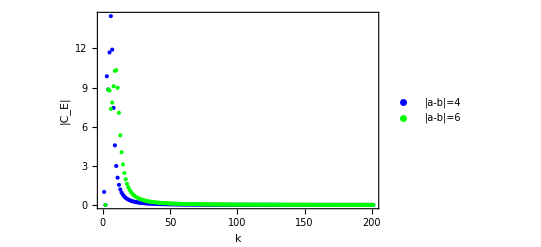

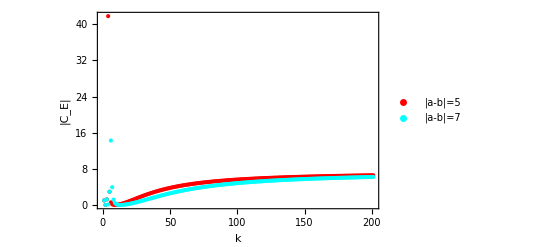

```mathematica
ListPlot[{Table[Limit[capacityChernSimons[6,2,2,kp],kp->k],{k,Range[0,200,1]}],Table[Limit[capacityChernSimons[8,2,2,kp],kp->k],{k,Range[0,200,1]}]},PlotStyle->{Blue,Green},PlotRange->Full,Frame->True,FrameLabel->{Style["k",20,Black],Style["|C_E|",20,Black]},PlotLegends->{"|a-b|=4","|a-b|=6"},LabelStyle->Directive[ Black,18]]
ListPlot[{Table[Limit[capacityChernSimons[7,2,2,kp],kp->k],{k,Range[0,200,1]}],Table[Limit[capacityChernSimons[9,2,2,kp],kp->k],{k,Range[0,200,1]}]},PlotStyle->{Red,Cyan},PlotRange->Full,Frame->True,FrameLabel->{Style["k",20,Black],Style["|C_E|",20,Black]},PlotLegends->{"|a-b|=5","|a-b|=7"},LabelStyle->Directive[ Black,18]]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/CE_SU2_WZW_amb_even.pdf",%39]
Export["/Users/aneekphys/Documents/modular plots/CE_SU2_WZW_amb_odd.pdf",%40]
```

/Users/aneekphys/Documents/modular plots/CE_SU2_WZW_amb_even.pdf

/Users/aneekphys/Documents/modular plots/CE_SU2_WZW_amb_odd.pdf

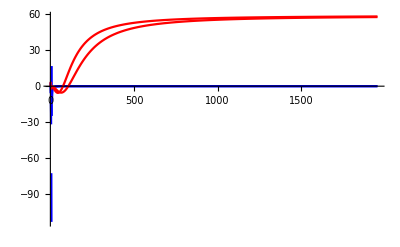

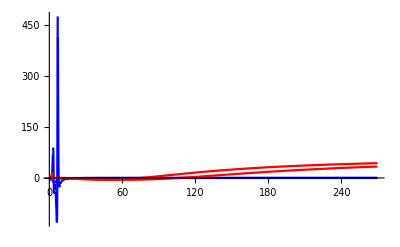

```mathematica
Plot[{Re[capacityChernSimons[6,2,5,k]],Re[capacityChernSimons[8,2,5,k]],Re[capacityChernSimons[7,2,5,k]],Re[capacityChernSimons[9,2,5,k]]},{k,1,1955},PlotRange->All,PlotStyle->{Blue,Blue,Red,Red}]
Plot[{Re[capacityChernSimons[6,2,5,k]],Re[capacityChernSimons[8,2,5,k]],Re[capacityChernSimons[7,2,5,k]],Re[capacityChernSimons[9,2,5,k]]},{k,1,270},PlotRange->All,PlotStyle->{Blue,Blue,Red,Red}]
```

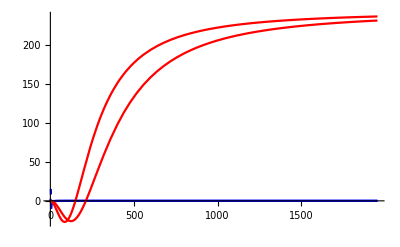

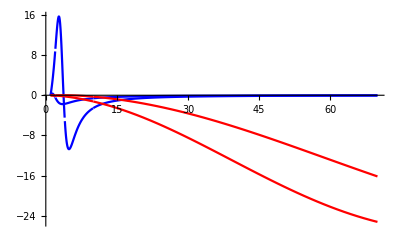

```mathematica
Plot[{Re[capacityChernSimons[6,2,10,k]],Re[capacityChernSimons[8,2,10,k]],Re[capacityChernSimons[7,2,10,k]],Re[capacityChernSimons[9,2,10,k]]},{k,1,1955},PlotRange->All,PlotStyle->{Blue,Blue,Red,Red}]
Plot[{Re[capacityChernSimons[6,2,10,k]],Re[capacityChernSimons[8,2,10,k]],Re[capacityChernSimons[7,2,10,k]],Re[capacityChernSimons[9,2,10,k]]},{k,1,70},PlotRange->All,PlotStyle->{Blue,Blue,Red,Red}]
```

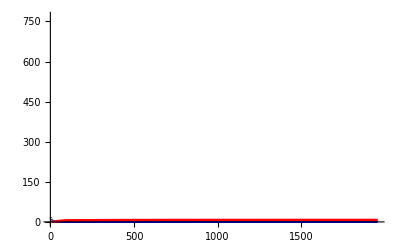

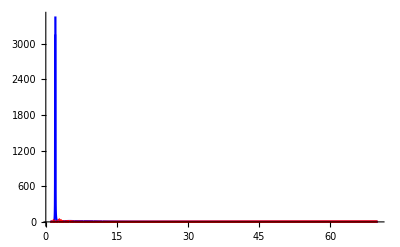

```mathematica
Plot[{Re[capacityChernSimons[6,2,2,k]],Re[capacityChernSimons[8,2,2,k]],Re[capacityChernSimons[7,2,2,k]],Re[capacityChernSimons[9,2,2,k]]},{k,1,1955},PlotRange->All,PlotStyle->{Blue,Blue,Red,Red}]
Plot[{Re[capacityChernSimons[6,2,2,k]],Re[capacityChernSimons[8,2,2,k]],Re[capacityChernSimons[7,2,2,k]],Re[capacityChernSimons[9,2,2,k]]},{k,1,70},PlotRange->All,PlotStyle->{Blue,Blue,Red,Red}]
```

## (SU(2))_k WZW model

```mathematica
x = Sqrt[2/(2+k)] Sin[Pi/(2+k)];
q = Exp[(2 Pi I)/(k+2)];
al = (q^(1/2))^Abs[a-b];
bet = (Exp[I Pi] q^(-1/2))^Abs[a-b];
alt = box[3,q]/box[2,q];
bett = box[1,q]/box[2,q];
```

```mathematica
avn[n_]:= (Log[al]^n al alt + Log[bet]^n bet bett)/(al alt + bet bett);
```

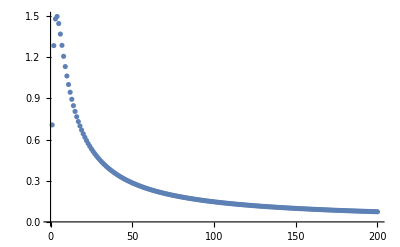

```mathematica
ListPlot[Re[Table[(x-avn[1])/.{k->kp,a->2,b->3},{kp,Range[1,200]}]],PlotRange->All]
```

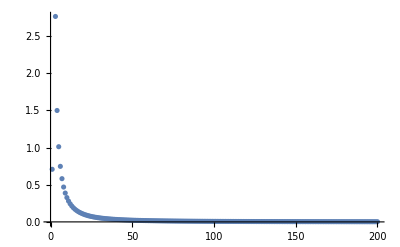

```mathematica
ListPlot[Re[Table[Limit[(x-avn[1])/.{a->2,b->4},k->kp],{kp,Range[1,200]}]],PlotRange->All]
```

```mathematica
a0 = x - avn[1];
b1 = Sqrt[avn[2]-avn[1]^2];
a1 = x - (avn[1]^3+avn[3]-2avn[2]avn[1])/(avn[2]-avn[1]^2);
T = {{a0,b1},{b1,a1}};
{e1,e2}= Eigenvalues[T];
```

```mathematica
phi0 = (e2-a0)Exp[-I e1 s] - (e1-a0) Exp[-I e2 s];
phi1 = - b1 Exp[- I e1 s] + b1 Exp[-I e2 s];
CR[k_] = Abs[phi1]^2/(Abs[phi0]^2+ Abs[phi1]^2);
```

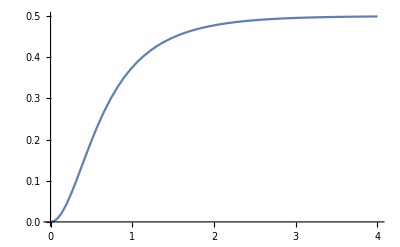

```mathematica
Plot[CR/.{a->3,b->2,k->2},{s,0,4}]
```

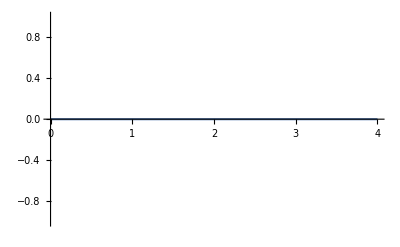

```mathematica
Plot[CR/.{a->3,b->2,k->1},{s,0,4}]
```

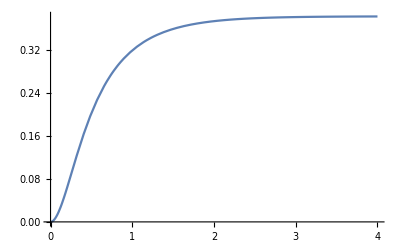

```mathematica
Plot[CR/.{a->3,b->2,k->3},{s,0,4}]
```

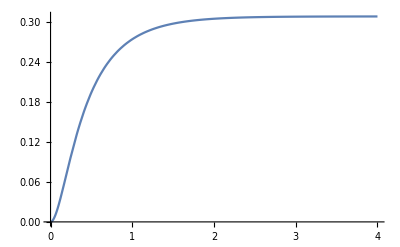

```mathematica
Plot[CR/.{a->3,b->2,k->5},{s,0,4},PlotRange->All]
```

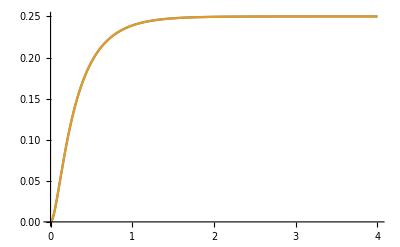

```mathematica
Plot[{CR/.{a->3,b->2,k->20000},CR/.{a->7,b->2,k->20000}},{s,0,4},PlotRange->All]
```

```mathematica
Plot[CR/.{a->4,b->2,k->1},{s,0,4},PlotRange->All]
```

-Graphics-

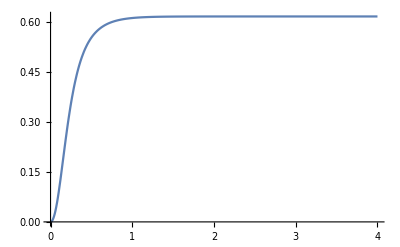

```mathematica
Plot[CR/.{a->6,b->2,k->3},{s,0,4},PlotRange->All]
```

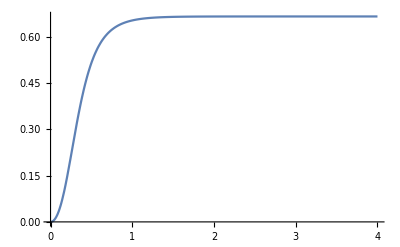

```mathematica
Plot[CR/.{a->4,b->2,k->4},{s,0,4},PlotRange->All]
```

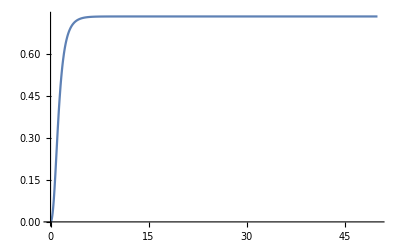

```mathematica
Plot[CR/.{a->4,b->2,k->10},{s,0,50},PlotRange->All]
```

```mathematica
b1/.{a->4,b->2,k->200}//N
```

0.000419115+0.0269463 ⅈ

```mathematica
Limit[b1,k->Infinity]
```

$Aborted

### SU2k WZW model

```mathematica
S[i_,j_,k_]:=(
Sqrt[2/(k+2)]Sin[(Pi (2 i +1 )(2 j +1))/(k+2)]
)
```

```mathematica
giveSECE[phiList_,psiList_,k_]:=(
S0i = Table[S[i,0,k],{i,Range[0,Length[phiList]-1,1]}];
n = Conjugate[phiList].psiList;
mom1 = 1/n Total[Table[Conjugate[phiList[[i]]] psiList[[i]] Log[(Conjugate[phiList[[i]]] psiList[[i]])/S0i[[i]]^2],{i,Range[1,Length[phiList],1]}]];
mom2 = 1/n Total[Table[Conjugate[phiList[[i]]] psiList[[i]] Log[(Conjugate[phiList[[i]]] psiList[[i]])/S0i[[i]]^2]^2,{i,Range[1,Length[phiList],1]}]];
mom3 = 1/n Total[Table[Conjugate[phiList[[i]]] psiList[[i]] Log[(Conjugate[phiList[[i]]] psiList[[i]])/S0i[[i]]^2]^3,{i,Range[1,Length[phiList],1]}]];
SE = Log[n]- mom1;
CE =mom2 - mom1^2;
a11 = Log[n]- (mom1^3+mom3 - 2 mom1 mom2)/(mom2 - mom1^2);
Return[{SE,CE,a11}]
);
```

```mathematica
delSECE[p1_,p2_]:=(
phiL1 = {Sqrt[p1],Sqrt[1-p1]};
phiL2= {Sqrt[p2],Sqrt[1-p2]};
{SE1,CE1} = giveSECE[phiL1,phiL1,2];
{SE2,CE2} = giveSECE[phiL2,phiL2,2];
{SE12,CE12} = giveSECE[phiL2,phiL1,2];

Return[{SE12 - 0.5 (SE1+SE2),CE12 - 0.5 (CE1+CE2)}]



);
```

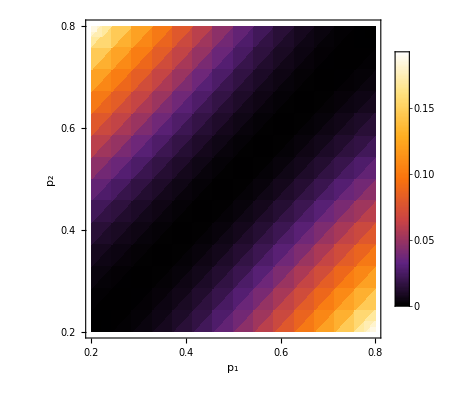

```mathematica
DensityPlot[delSECE[p1,p2][[1]],{p1,0.2,0.8},{p2,0.2,0.8},ColorFunction->"SunsetColors",PlotLegends->Automatic,Frame->True,FrameLabel->{Style["p_1",Black,24],Style["p_2",Black,24]},FrameTicks->{{{0.2,0.4,0.6,0.8},None},{{0.2,0.4,0.6,0.8},None}},FrameTicksStyle->Directive[Black,20],LabelStyle->Directive[Bold, Medium,15]]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/pseudo_entropy_excess_on_T2.pdf",%79,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/pseudo_entropy_excess_on_T2.pdf

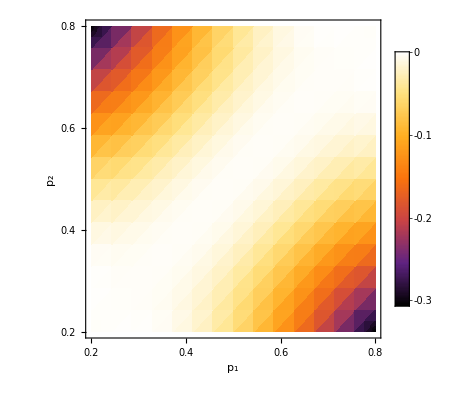

```mathematica
DensityPlot[delSECE[p1,p2][[2]],{p1,0.2,0.8},{p2,0.2,0.8},ColorFunction->"SunsetColors",PlotLegends->Automatic,MaxRecursion->6,Frame->True,FrameLabel->{Style["p_1",Black,24],Style["p_2",Black,24]},FrameTicks->{{{0.2,0.4,0.6,0.8},None},{{0.2,0.4,0.6,0.8},None}},FrameTicksStyle->Directive[Black,20],LabelStyle->Directive[Bold, Medium,15]]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/pseudo_capacity_excess_on_T2.pdf",%,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/pseudo_capacity_excess_on_T2.pdf

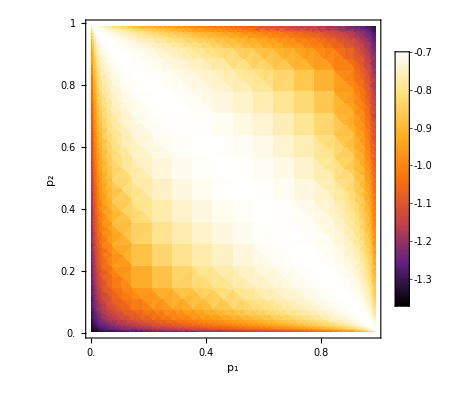

```mathematica
DensityPlot[giveSECE[{Sqrt[p2],Sqrt[1-p2]},{Sqrt[p1],Sqrt[1-p1]},2][[1]],{p1,0.002,0.99},{p2,0.002,0.99},PlotLegends->Automatic,ColorFunction->"SunsetColors",MaxRecursion->6,Frame->True,FrameLabel->{Style["p_1",Black,24],Style["p_2",Black,24]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1},None},{{0.0,0.2,0.4,0.6,0.8,1},None}},FrameTicksStyle->Directive[Black,20],LabelStyle->Directive[Bold, Medium,15]]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/pseudo_entropy_on_T2.pdf",%91,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/pseudo_entropy_on_T2.pdf

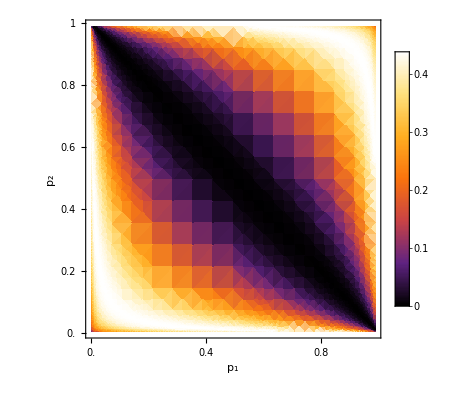

```mathematica
DensityPlot[giveSECE[{Sqrt[p2],Sqrt[1-p2]},{Sqrt[p1],Sqrt[1-p1]},2][[2]],{p1,0.002,0.99},{p2,0.002,0.99},PlotLegends->Automatic,ColorFunction->"SunsetColors",MaxRecursion->6,Frame->True,FrameLabel->{Style["p_1",Black,24],Style["p_2",Black,24]},FrameTicks->{{{0.0,0.2,0.4,0.6,0.8,1},None},{{0.0,0.2,0.4,0.6,0.8,1},None}},FrameTicksStyle->Directive[Black,20],LabelStyle->Directive[Bold, Medium,15]]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/pseudo_capacity_on_T2.pdf",%,ImageResolution->1000]
```

/Users/aneekphys/Documents/modular plots/pseudo_capacity_on_T2.pdf

```mathematica
2 Log[S[0,0,2]]//N
```

-1.38629

```mathematica
T = {{a0,b1},{b1,a1}};
{e1,e2}= Eigenvalues[T];
phi0 = (e2-a0)Exp[-I e1 s] - (e1-a0) Exp[-I e2 s];
phi1 = - b1 Exp[- I e1 s] + b1 Exp[-I e2 s];
CR= Abs[phi1]^2/(Abs[phi0]^2+ Abs[phi1]^2);
```

```mathematica
psilist = {Sqrt[p1],Sqrt[1-p1]};
philist = {Sqrt[p2],Sqrt[1-p2]};
```

```mathematica
{a0,b1sq,a1} = giveSECE[philist,psilist,2];
```

```mathematica
b1 = Sqrt[b1sq]
```

√(-((√(1-p1) Conjugate[√(1-p2)] Log[4 √(1-p1) Conjugate[√(1-p2)]]+√p1 Conjugate[√p2] Log[4 √p1 Conjugate[√p2]])^2/(√(1-p1) Conjugate[√(1-p2)]+√p1 Conjugate[√p2])^2)+(√(1-p1) Conjugate[√(1-p2)] Log[4 √(1-p1) Conjugate[√(1-p2)]]^2+√p1 Conjugate[√p2] Log[4 √p1 Conjugate[√p2]]^2)/(√(1-p1) Conjugate[√(1-p2)]+√p1 Conjugate[√p2]))

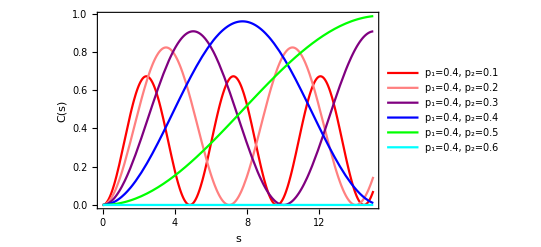

```mathematica
Plot[{CR/.{p1->0.4,p2->0.1},CR/.{p1->0.4,p2->0.2},CR/.{p1->0.4,p2->0.3},CR/.{p1->0.4,p2->0.4},CR/.{p1->0.4,p2->0.5},CR/.{p1->0.4,p2->0.6}},{s,0,15},Frame->True,PlotStyle->{Red,Pink,Purple,Blue,Green,Cyan},LabelStyle->Directive[Bold, Medium,Black,15],FrameLabel->{Style["s",22,Black],Style["C(s)",22,Black]},PlotLegends->{"p_1=0.4, p_2=0.1","p_1=0.4, p_2=0.2","p_1=0.4, p_2=0.3","p_1=0.4, p_2=0.4","p_1=0.4, p_2=0.5","p_1=0.4, p_2=0.6"}]
```

```mathematica
Export["/Users/aneekphys/Documents/modular plots/pseudo-complexity_on_T2.pdf",%]
```

/Users/aneekphys/Documents/modular plots/pseudo-complexity_on_T2.pdf